### Global Variables

```mathematica
DIR = "/home/hfl/ldata/edu/cs370_deep_learning/final_project/";
TENSORDIR = StringJoin@{DIR, "tensors/"};
file = ReadList[StringJoin@{DIR, "info/64_test_fast_delta-1"}, String];
```

### I/O: Read in file contents

```mathematica
ParseFile[contents_] := Module[
{i, j,k,v,data = {}, entry=Association[], comments=Association[], state=0, list,tensor,info},

For[i = 1, i <= Length[contents], i+=1,
(* parse comments *)
If[StringMatchQ[contents[[i]], StartOfString~~"#"~~__],
info=StringSplit[StringDrop[contents[[i]], 1],";"];

For[j=1,j ≤ Length[info], j+=1,
{k,v}=StringTrim/@StringSplit[info[[j]],":"];
(* convert to list of numbers unless it's type *)
If[k == "type",
AppendTo[comments,k -> v],
AppendTo[comments, k-> ReadList[StringToStream[v], Number]]
];
];
Continue[];
];

If[state== 0,
(* state == 0 -> parse the dimensions *)
AppendTo[entry, "shape"-> ReadList[StringToStream[contents[[i]]], Number]],

(* state == 1 -> read in data from file name that was read in *)
list = ReadList[StringJoin@{TENSORDIR,  contents[[i]]}, Number, RecordLists->True];
tensor = ArrayReshape[list, entry[["shape"]]];
AppendTo[entry, "tensor"-> tensor];
AppendTo[entry, "info"-> comments];
AppendTo[data, entry];

Print["[",Length[data], "] Read ", comments[["type"]], " domain from \"", contents[[i]], "\"."];

(* reset accumulators *)
entry=Association[];
comments=Association[];
];

(* update state for next iteration *)
state = Mod[state+1,2];
];
Print["Done."];
data
];
```

### Procedures for Visualizing Domains/Fields

```mathematica
GetDomainShape[index_, dataset_]:= Module[
{info,r,l,x,y,z,dx,dy,dz, shape},
info = dataset[[index,"info"]];

shape = Switch[info[["type"]],
(* return cylinder if type if cylinder *)
"cylinder",
{r,l}=info[["dim"]];
{z,y,x}=info[["pos"]];
Cylinder[{{z+0.5,y-l,x+0.5},{z+0.5,y+l+1,x+0.5}}, r],

(* return cuboid if type is box *)
"box",
{z,y,x}=info[["pos"]];
{dz,dy,dx}=info[["dim"]];
Cuboid[{z-dz,y-dy,x-dx},{z+dz+1,y+dy+1,x+dx+1}],

(* return sphere if type if sphere *)
"sphere",
{z,y,x}=info[["pos"]];
{r}=info[["radius"]];
Sphere[{z+0.5,y+0.5,x+0.5}, r]
];

shape
];
PrintDomainInfo[index_,dataset_]:=Module[{},
Print[dataset[[index,"info"]],"\n"]
];
```

```mathematica
DomainMesh[index_, dataset_, bd_] := Module[{domain,shape,mesh,pts,cells},
shape=dataset[[index,"shape"]];
domain = GetDomainField[index, dataset, "v-cond-mask"][[bd+1;;-bd-1,bd+1;;-bd-1,bd+1;;-bd-1]];
domain=ArrayPad[domain,bd];
(*Print[domain[[;;,35,1;;10]]];*)
mesh =ArrayMesh[domain,DataRange->{{0,shape[[-3]]},{0,shape[[-1]]},{0,shape[[-2]]}}];
pts = ({#[[1]],shape[[-2]]-#[[3]],#[[2]]})&/@MeshCoordinates[mesh];
cells = MeshCells[mesh, 2];
MeshRegion[pts,cells, MeshCellStyle->{1-> None}]
];
```

```mathematica
GetDomainField[index_, dataset_, name_]:=Module[
{field,data,mask},
data = dataset[[index,"tensor"]];
field = Switch[name,
(* return field a, whose curl gives the velocity field *)
"a",
Transpose[data[[1;;3]],{4,1,2,3}],

(* return the velocity field *)
"v",
Transpose[data[[4;;6]],{4,1,2,3}],

(* return the pressure field *)
"p",
data[[7]],

(* return field of boundary condition for v *)
"v-cond",
Transpose[data[[8;;10]],{4,1,2,3}],

(* return mask for v boundary conditions *)
"v-cond-mask",
data[[11]],

(* return masked field of boundary condition for v *)
"v-cond-masked",
mask=ArrayReshape[data[[11]],Append[Dimensions@data[[11]],1]];
Transpose[data[[8;;10]],{4,1,2,3}]*Join[mask,mask,mask,4]
];

field
];
```

```mathematica
SliceDomain2D[index_, dataset_, name_, axis_,vals_]:=Module[
{info, z0,z1,x0,x1,z,y,x,dz,dx,dy,r,l,field},
info=dataset[[index, "info"]];
field=GetDomainField[index, dataset, name];
If[name=="p",
(*scalar field*)
Switch[axis,
"Y",
Transpose[field[[;;,vals,;;]], {2,1,3}],
"X",
Transpose[field[[;;,;;,vals]], {3,2,1}],
"Z",
field[[vals,;;,;;]]
]
,
(* vector field *)
Switch[axis,
"Y",
Transpose[field[[;;,vals,;;,{1,3}]], {2,1,3,4}],
"X",
Transpose[field[[;;,;;,vals,{1,2}]], {3,1,2,4}],
"Z",
field[[vals,;;,;;,{2,3}]]
]
]
];
```

```mathematica
GetShapeRegion[index_,dataset_]:= Module[
{info,type,z0,y0,x0,r,l,surface},
info=dataset[[index,"info"]];
{z0,y0,x0}=info[["pos"]]+{0.5,0,0.5};

surface=Switch[info[["type"]],
"cylinder",
{r,l}=info[["dim"]];
RegionUnion[ImplicitRegion[(z-z0)^2+(x-x0)^2==r^2,
{{z,z0-r,z0+r}, {y,y0-l,y0+l+1},{x,x0-r,x0+r}}],
ImplicitRegion[(z-z0)^2+(x-x0)^2≤ r^2 ,
{{z,z0-r,z0+r}, {y,y0-l,y0-l},{x,x0-r,x0+r}}],
ImplicitRegion[(z-z0)^2+(x-x0)^2≤ r^2 ,
{{z,z0-r,z0+r}, {y,y0+l+1,y0+l+1},{x,x0-r,x0+r}}]]
];

surface
];
```

```mathematica
dataset=ParseFile[file];
```

[1] Read cylinder domain from "tensor-2021-04-25_04_56_42.494289".

[2] Read cylinder domain from "tensor-2021-04-25_04_56_50.214951".

[3] Read cylinder domain from "tensor-2021-04-25_04_56_58.484239".

[4] Read cylinder domain from "tensor-2021-04-25_04_57_06.416708".

[5] Read cylinder domain from "tensor-2021-04-25_04_57_14.579160".

[6] Read cylinder domain from "tensor-2021-04-25_04_57_22.962350".

[7] Read cylinder domain from "tensor-2021-04-25_04_57_30.849142".

[8] Read cylinder domain from "tensor-2021-04-25_04_57_38.965833".

[9] Read cylinder domain from "tensor-2021-04-25_04_57_47.169334".

[10] Read cylinder domain from "tensor-2021-04-25_04_57_55.387550".

[11] Read cylinder domain from "tensor-2021-04-25_04_58_03.220327".

[12] Read cylinder domain from "tensor-2021-04-25_04_58_11.846121".

[13] Read cylinder domain from "tensor-2021-04-25_04_58_19.784629".

[14] Read cylinder domain from "tensor-2021-04-25_04_58_28.092866".

[15] Read cylinder domain from "tensor-2021-04-25_04_58_36.234809".

[16] Read cylinder domain from "tensor-2021-04-25_04_58_44.645769".

[17] Read cylinder domain from "tensor-2021-04-25_04_58_52.419459".

[18] Read cylinder domain from "tensor-2021-04-25_04_59_00.563497".

[19] Read cylinder domain from "tensor-2021-04-25_04_59_08.944850".

[20] Read cylinder domain from "tensor-2021-04-25_04_59_16.813146".

[21] Read cylinder domain from "tensor-2021-04-25_04_59_24.983977".

Done.

```mathematica
index=20;
dim=Dimensions[GetDomainField[index, dataset, "p"]];
range=({0,#})&/@dim
```

{{0,32},{0,32},{0,64}}

```mathematica
Show[
(*Graphics3D[{Opacity[0.5],GetDomainShape[index, dataset]}],*)
Graphics3D[{Opacity[0.5],DomainMesh[index,dataset,5]}],
ListVectorPlot3D[
GetDomainField[index,dataset,"v"], 
VectorPoints-> Automatic,
VectorStyle->Arrowheads[{0.015}],
PlotRange->({0,#})&/@dim
],
Axes-> True,
PlotRange->range,
BoxRatios-> Automatic,
AxesLabel->{"z","y","x"}
]
PrintDomainInfo[index,dataset]
```

-Graphics3D-

<|v_flow→{-1},type→cylinder,pos→{15.,15.,27.},velocity→{0,0,1},omega→{2},dim→{6,6}|>

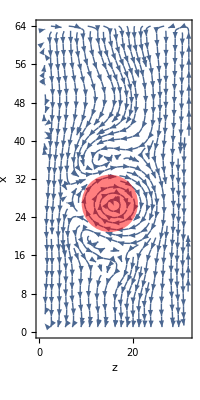

```mathematica
axis=2;
Show[
ListStreamPlot[SliceDomain2D[index, dataset, "v", {"Z","Y","X"}[[axis]], {15}],
FrameLabel-> Drop[{"z","y","x"},{axis}],
PlotRange-> Drop[range,{axis}],
StreamPoints->Fine,
AspectRatio-> Automatic
],
(*Graphics[{Black, Opacity[0.5], Rectangle[{16-6,25-6}, {16+6,25+6}]}]*)
Graphics[{Red, Opacity[0.5],Disk[{15,27},6]}]
]
```

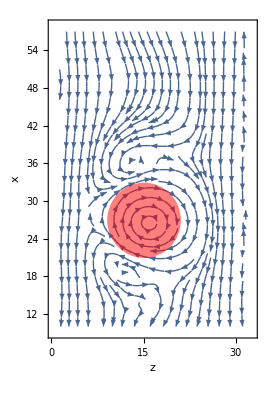

```mathematica
axis=2;
slicerange={{1,32},{10,57}};
Show[
ListStreamPlot[SliceDomain2D[index, dataset, "v", {"Z","Y","X"}[[axis]], {15}]
[[;;,slicerange[[1,1]];; slicerange[[1,2]], slicerange[[2,1]];; slicerange[[2,2]]]],
FrameLabel-> Drop[{"z","y","x"},{axis}],
DataRange->slicerange,
AspectRatio-> Automatic
],
Graphics[{Red, Opacity[0.5],Disk[{15,27},6]}]
(*Graphics[{Black, Opacity[0.5], Rectangle[{16-6,25-6}, {16+6,25+6}]}]*)
]
```

```mathematica
axis=2;
slicerange={{1,32},{10,55}};
Show[
ListDensityPlot[
Transpose[
SliceDomain2D[index, dataset, "p", {"Z","Y","X"}[[axis]], {15}][[1,slicerange[[1,1]];; slicerange[[1,2]], slicerange[[2,1]];; slicerange[[2,2]]]],
{2,1}],
DataRange->slicerange,
FrameLabel-> Drop[{"z","y","x"},{axis}],
ColorFunction->"TemperatureMap",
PlotLegends->Automatic,
AspectRatio-> Automatic
],
Graphics[{Black, Opacity[0.8],Disk[{16,26},6]}]
(*Graphics[{Black, Opacity[0.5], Rectangle[{16-6,25-6}, {16+6,25+6}]}]*)
]
```

-Graphics-

```mathematica
axis=2;
Show[
ListDensityPlot[
Transpose[
SliceDomain2D[index, dataset, "p", {"Z","Y","X"}[[axis]], {15}][[1]],
{2,1}],
FrameLabel-> Drop[{"z","y","x"},{axis}],
PlotRange-> Drop[range,{axis}],
ColorFunction->"TemperatureMap",
PlotLegends->Automatic,
AspectRatio-> Automatic
],
Graphics[{Black, Opacity[0.8],Disk[{16,26},6]}]
]
```

-Graphics-

```mathematica
bd=0;
Show[
Graphics3D[{Opacity[0.5],GetDomainShape[index, dataset]}],
(*Graphics3D[{Opacity[0.5],DomainMesh[index,dataset,5]}],*)
ListDensityPlot3D[
GetDomainField[index,dataset,"p"],
ColorFunction->"TemperatureMap",PlotLegends->Automatic,
DataRange-> range
],
PlotRange->range,
Axes-> True,
BoxRatios-> Automatic,
AxesLabel->{"z","y","x"}
]
```

-Graphics3D-

```mathematica
index=19;
```

```mathematica
Show[
Graphics3D[GetDomainShape[index, dataset]],
ListSliceVectorPlot3D[
GetDomainField[index,dataset,"v"], 
{
"CenterPlanes"
(*{"XStackedPlanes", {32}}*)
},
VectorPoints-> Fine,
DataRange-> range
],
Axes-> True,
PlotRange->range,
BoxRatios-> Full,
AxesLabel->{"z","y","x"}
]
```

-Graphics3D-